```mathematica
Needs["PlotLegends`"]
```

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
fticks=Table[{l*1000,ToString[l*1000],{0,.01}},{l,1,7}]
```

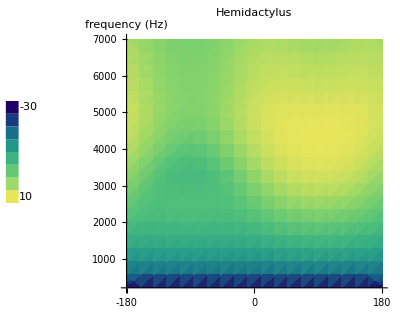

```mathematica
ShowLegend[DensityPlot[20*Log10[ω*Abs[SL]/(Pi*atymp*atymp)],{θ,-180,180},{f,200,7000},ColorFunction->"BlueGreenYellow",PlotPoints->20,Frame->False,Axes->True,AxesOrigin->{-180,200},AxesLabel->{None,"frequency (Hz)"},Ticks->{dticks,fticks},PlotLabel->"Hemidactylus",FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,8,"-30","10",LegendPosition->{-1.5,-.35},LegendOrientation->Vertical}]
```

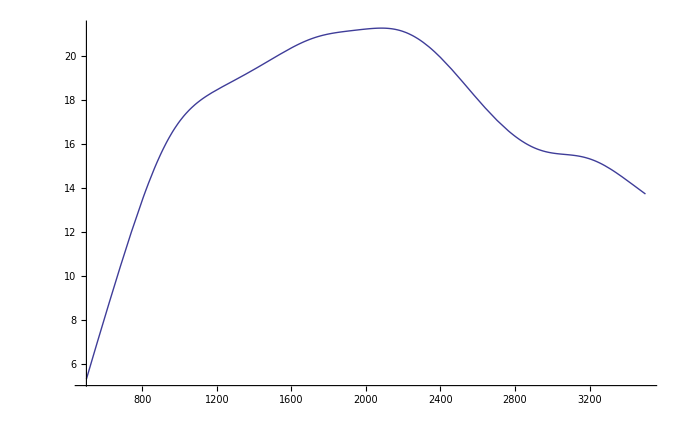

```mathematica
Plot[20*Log10[ω*Abs[SL]/(Pi*atymp*atymp)]/.θ->90,{f,500,3500}]
```

```mathematica
+
```

```mathematica
20*Log10[ω*Abs[SL]/(Pi*atymp*atymp)]/.{θ->-90,f->50}
```

-31.9086

```mathematica
dticks=Table[{(l-1)*90-180,ToString[(l-1)*90-180],{0,.01}},{l,1,5}]
fticks=Table[{l*500,ToString[l*500],{0,.01}},{l,1,7}]
```

{{-180,-180,{0,0.01}},{-90,-90,{0,0.01}},{0,0,{0,0.01}},{90,90,{0,0.01}},{180,180,{0,0.01}}}

{{500,500,{0,0.01}},{1000,1000,{0,0.01}},{1500,1500,{0,0.01}},{2000,2000,{0,0.01}},{2500,2500,{0,0.01}},{3000,3000,{0,0.01}},{3500,3500,{0,0.01}}}

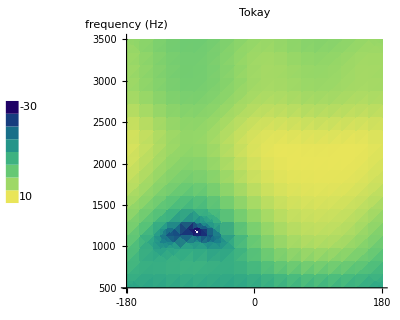

```mathematica
ShowLegend[DensityPlot[20*Log10[ω*Abs[SL]/(10*Pi*atymp*atymp)],{θ,-180,180},{f,
500,3500},ColorFunction->"BlueGreenYellow",PlotPoints->20,PlotRange->35,Frame->False,Axes->True,AxesOrigin->{-180,500},AxesLabel->{None,"frequency (Hz)"},Ticks->{dticks,fticks},PlotLabel->"Tokay",FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,8,"-30","10",LegendPosition->{-1.5,-.35},LegendOrientation->Vertical}]
```